```mathematica
Clear["Global`*"];
Off[NIntegrate::ncvb];
```

```mathematica
T0=0.5;(* ps *)
λ0=1.060;(* mkm *)
γ=5.5;(* 1/W *)
CalcWindow=7;(* ps *)
N0=2^11-1;
L=0.5;(* km *)
h = 0.002;(* km *)
P=8.7;(* W *)
```

```mathematica
Frequency2Wavelength[λ0var_,CalcWindowvar_,N0var_]:=(LightSpeed=3×10^5;Return[ParallelTable[N[10^6 10^3(2 π LightSpeed)/(Δω+(2 π LightSpeed)/(λ0var×10^-6×10^-3))], {Δω, -π/(CalcWindowvar×10^-12)×(N0var-1)/2,π/(CalcWindowvar×10^-12)×(N0var-1)/2,π/(CalcWindowvar×10^-12)}]]);
```

```mathematica
WavelengthArray = Frequency2Wavelength[λ0,CalcWindow,N0];
TimeArray=ParallelTable[N[t],{t,-CalcWindow, +CalcWindow,(2 CalcWindow)/(N0-1)}];
```

```mathematica
PreGaussImp=ParallelTable[N[Exp[-(t^2(2 √(2Log[2]))^2)/(2 T0^2)]],{t,-CalcWindow, +CalcWindow,(2 CalcWindow)/(N0-1)}];
```

```mathematica
GaussImp=PreGaussImp×√P/√NIntegrate[Interpolation[Transpose[{Table[t,{t,-CalcWindow, +CalcWindow,(2 CalcWindow)/(N0-1)}],PreGaussImp^2}],InterpolationOrder->1][x],{x,-CalcWindow, +CalcWindow}];
```

```mathematica
SpatialOp[x_List]=Exp[I γ Abs[x]^2 L];
```

```mathematica
Imp = SpatialOp[GaussImp];
```

```mathematica
PulseIn=Transpose[{TimeArray,Abs[GaussImp]^2}];
PulseOut=Transpose[{TimeArray,Abs[Imp]^2}];
SpectrumIn=Transpose[{WavelengthArray,RotateLeft[Abs[Fourier[GaussImp]]^2,(N0-1)/2]}];
SpectrumOut=Transpose[{WavelengthArray,RotateLeft[Abs[Fourier[Imp]]^2,(N0-1)/2]}];
```

```mathematica
TempImp=RotateLeft[Fourier[Imp],(N0-1)/2];
ImpSpectrumSelected=RotateRight[Table[If[1.18<SpectrumOut[[i,1]]<1.25,TempImp[[i]],0],{i,1,N0}],(N0-1)/2];
ImpSelected=InverseFourier[ImpSpectrumSelected];
```

```mathematica
PulseSelected=Transpose[{TimeArray,Abs[ImpSelected]^2}];
SpectrumSelected=Transpose[{WavelengthArray,RotateLeft[Abs[Fourier[ImpSelected]]^2,(N0-1)/2]}];
```

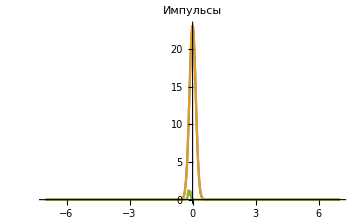
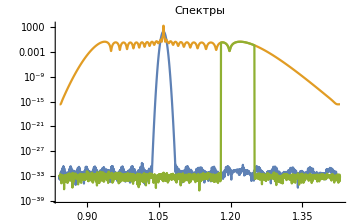

```mathematica
{ListPlot[{PulseIn,PulseIn,PulseSelected},PlotRange->All,Joined->True,ImageSize->Medium,PlotLabel->"Импульсы"],
ListLogPlot[{SpectrumIn,SpectrumOut,SpectrumSelected},PlotRange->{Full,Full},Joined->True,ImageSize->Medium,PlotLabel->"Спектры"]}
```

λ = 1100 nm; P = 1.0; L = 1.35; 1.09<SpectrumOut[[i,1]]<1.14;
λ = 1200 nm; P = 1.0; L = 3.90; 1.18<SpectrumOut[[i,1]]<1.25;
λ = 1500 nm; P = 4.6; L = 2.00; 1.45<SpectrumOut[[i,1]]<1.55;
λ =   700 nm; P = 8.7; L = 2.00; 0.69<SpectrumOut[[i,1]]<0.71; CalcWindow = 2;